```mathematica
Clear["Global`*"]
```

```mathematica
r[t_] = {3Cos[3.3π*t], Sin[4π*t] + 4*t}
```

{3 Cos[10.3673 t],4 t+Sin[4 π t]}

```mathematica
r[0]
```

{3.,0}

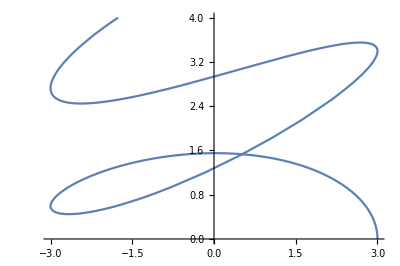

```mathematica
track =ParametricPlot[r[t], {t, 0, 1}, AxesLabel-> {"x", "y", "z"}, PlotRange->All]
```

```mathematica
cauchy = Graphics[Point[r[1]]];
```

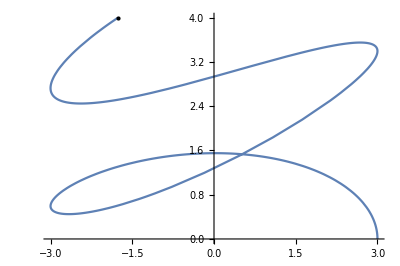

```mathematica
Show[track, cauchy]
```